```mathematica
s=NDSolve[{x''[t]==4y'[t]+2.2237606348101603 10^-16x'''[t],y''[t]==-4x'[t]+2.2237606348101603 10^-16y'''[t],z''[t]==10^-16z'''[t],x[0]==-3,y[0]==3,z[0]==0,x'[0]==1,y'[0]==2,z'[0]==0.1,x''[0]==8,y''[0]==-4,z''[0]==0},{x[t],y[t],z[t],x'[t],y'[t],z'[t],x''[t],y''[t],z''[t]},{t,0,10000}]
ParametricPlot3D[{x[t],y[t],z[t]}/.s,{t,0,5},AxesLabel->{x,y,z}]
ParametricPlot3D[{x[t],y[t],z[t]}/.s,{t,9995,10000},AxesLabel->{x,y,z}]
```

{{x[t]→InterpolatingFunction[{{0., 10000.}}, <>][t],y[t]→InterpolatingFunction[{{0., 10000.}}, <>][t],z[t]→InterpolatingFunction[{{0., 10000.}}, <>][t],x'[t]→InterpolatingFunction[{{0., 10000.}}, <>][t],y'[t]→InterpolatingFunction[{{0., 10000.}}, <>][t],z'[t]→InterpolatingFunction[{{0., 10000.}}, <>][t],x''[t]→InterpolatingFunction[{{0., 10000.}}, <>][t],y''[t]→InterpolatingFunction[{{0., 10000.}}, <>][t],z''[t]→InterpolatingFunction[{{0., 10000.}}, <>][t]}}

-Graphics3D-

-Graphics3D-

```mathematica
s0=DSolve[{x''[t]==4y'[t],y''[t]==-4x'[t],z''[t]==0,x'[0]==1,y'[0]==2,z'[0]==0.1,x[0]==-3,y[0]==3,z[0]==0},{x[t],y[t],z[t]},t]
ParametricPlot3D[{x[t],y[t],z[t]}/.s0,{t,0,2},AxesLabel->{x,y,z}]
```

{{x[t]→1/4 (-10-2 Cos[4 t]+Sin[4 t]),y[t]→1/4 (11+Cos[4 t]+2 Sin[4 t]),z[t]→0.1 t}}

-Graphics3D-

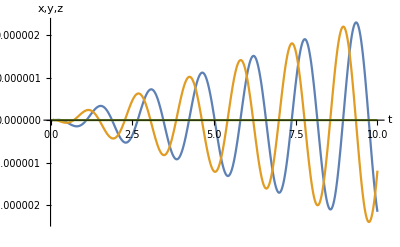

```mathematica
Plot[{Evaluate[{x[t]}/.s]-Evaluate[{x[t]}/.s0],Evaluate[{y[t]}/.s]-Evaluate[{y[t]}/.s0],Evaluate[{z[t]}/.s]-Evaluate[{z[t]}/.s0]},{t,0,10},AxesLabel->{t,"x,y,z"}]
```

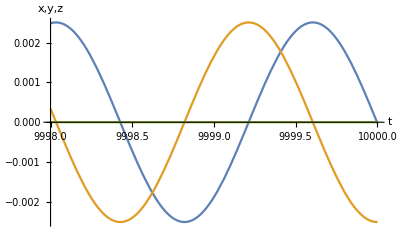

```mathematica
Plot[{Evaluate[{x[t]}/.s]-Evaluate[{x[t]}/.s0],Evaluate[{y[t]}/.s]-Evaluate[{y[t]}/.s0],Evaluate[{z[t]}/.s]-Evaluate[{z[t]}/.s0]},{t,9998,10000},AxesLabel->{t,"x,y,z"}]
```

```mathematica
FindMinimum[Norm[Evaluate[{x[t],y[t],z[t]}/.s0]],{t,1}]
```

{3.15872,{t→0.877468}}